## Subroutines for quantum computing

```mathematica
Needs["QDENSITY`Qdensity`"]
```

```mathematica
Needs["QDENSITY`QCWave`"]
```

## Refocusing pulses to correct errors in two-qubit gates

### Ising interaction

```mathematica
α=.;
θ=.;
ϵ=.;

Ux=MatrixExp[-I α/2 AF[𝕀⊗s[1]]];
UxAl=Ux/.{α->-α};
Ux2Al=Ux/.{α->2α};

Uzz=MatrixExp[-I θ(1+ϵ)AF[s[3]⊗s[3]]];
Uzz2Pi=Uzz/.{θ->-2Pi};
Uzz0=Uzz/.{ϵ->0};

Vzz=UxAl.Uzz2Pi.Ux2Al.Uzz2Pi.UxAl.Uzz;

fzz=Tr[Uzz.Adj[Uzz0]]/Tr[Uzz0.Adj[Uzz0]];
Fzz=Tr[Vzz.Adj[Uzz0]]/Tr[Uzz0.Adj[Uzz0]];

θ=4Pi Cos[α];

Print["(δU_zz)_12=",FullSimplify[Series[Refine[Vzz[[1,2]]-Uzz0[[1,2]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["(δU_zz)_21=",FullSimplify[Series[Refine[Vzz[[2,1]]-Uzz0[[2,1]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["(δU_zz)_34=",FullSimplify[Series[Refine[Vzz[[3,4]]-Uzz0[[3,4]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["(δU_zz)_43=",FullSimplify[Series[Refine[Vzz[[4,3]]-Uzz0[[4,3]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["1-f_2^zz=",FullSimplify[Series[Refine[1-fzz,Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,3}]]]
Print["1-F_2^zz=",FullSimplify[Series[Refine[1-Fzz,Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,5}]]]
```

(δU_zz)_12=-8 ⅈ ⅇ^(4 ⅈ π Cos[α]) π^2 Cos[α] Sin[α]+O[ϵ]^1

(δU_zz)_21=-4 ⅈ ⅇ^(-4 ⅈ π Cos[α]) π^2 Sin[2 α]+O[ϵ]^1

(δU_zz)_34=-4 ⅈ ⅇ^(-4 ⅈ π Cos[α]) π^2 Sin[2 α]+O[ϵ]^1

(δU_zz)_43=-8 ⅈ ⅇ^(4 ⅈ π Cos[α]) π^2 Cos[α] Sin[α]+O[ϵ]^1

1-f_2^zz=8 π^2 Cos[α]^2 ϵ^2+O[ϵ]^4

1-F_2^zz=8 π^4 Sin[2 α]^2 ϵ^4+O[ϵ]^6

### XY interaction

```mathematica
α=.;
θ=.;
ϵ=.;

Uz=MatrixExp[-I α/2 AF[𝕀⊗s[3]]];
UzAl=Uz/.{α->-α};
Uz2Al=Uz/.{α->2α};

Uxy=MatrixExp[-I θ(1+ϵ)(AF[s[1]⊗s[1]]+AF[s[2]⊗s[2]])];
Uxy2Pi=Uxy/.{θ->-2Pi};
Uxy0=Uxy/.{ϵ->0};

Vxy=UzAl.Uxy2Pi.Uz2Al.Uxy2Pi.UzAl.Uxy;

fxy=Tr[Uxy.Adj[Uxy0]]/Tr[Uxy0.Adj[Uxy0]];
Fxy=Tr[Vxy.Adj[Uxy0]]/Tr[Uxy0.Adj[Uxy0]];

θ=4Pi Cos[α];

Print["(δU_xy)_22=",FullSimplify[Series[Refine[Vxy[[2,2]]-Uxy0[[2,2]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["(δU_xy)_23=",FullSimplify[Series[Refine[Vxy[[2,3]]-Uxy0[[2,3]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["(δU_xy)_32=",FullSimplify[Series[Refine[Vxy[[3,2]]-Uxy0[[3,2]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["(δU_xy)_33=",FullSimplify[Series[Refine[Vxy[[3,3]]-Uxy0[[3,3]],Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,2}]/ϵ^2]]
Print["1-f_2^xy=",FullSimplify[Series[Refine[1-fxy,Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,3}]]]
Print["1-F_2^xy=",FullSimplify[Series[Refine[1-Fxy,Assumptions->{α∈Reals,ϵ∈Reals}],{ϵ,0,5}]]]
```

(δU_xy)_22=16 ⅈ π^2 Cos[8 π Cos[α]] Sin[2 α]+O[ϵ]^1

(δU_xy)_23=16 π^2 Sin[2 α] Sin[8 π Cos[α]]+O[ϵ]^1

(δU_xy)_32=-16 (π^2 Sin[2 α] Sin[8 π Cos[α]])+O[ϵ]^1

(δU_xy)_33=-16 ⅈ π^2 Cos[8 π Cos[α]] Sin[2 α]+O[ϵ]^1

1-f_2^xy=16 π^2 Cos[α]^2 ϵ^2+O[ϵ]^4

1-F_2^xy=64 π^4 Sin[2 α]^2 ϵ^4+O[ϵ]^6

### Controlled phase interaction

```mathematica
α=.;
θ=.;
ϵ=.;

Uz=MatrixExp[I θ/4(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]])];
UxPi=MatrixExp[-I Pi/2(AF[s[1]⊗𝕀]+AF[𝕀⊗s[1]])];
UxAl=MatrixExp[I α/2 AF[𝕀⊗s[1]]];
Ux2Al=MatrixExp[-I α AF[𝕀⊗s[1]]];

Ucp=MatrixExp[-I θ/4(1+ϵ)(AF[𝕀⊗𝕀]-AF[s[3]⊗𝕀]-AF[𝕀⊗s[3]]+AF[s[3]⊗s[3]])];
Ucp2=Ucp/.{θ->2θ};
Ucp0=Ucp/.{ϵ->0};

Uex=UxPi.Ucp2.UxPi.Ucp2;
Uex2=Uex/.{θ->θ/4};
Uex2Pi=Uex/.{θ->-2Pi};

Vcp=Uz.UxAl.Uex2Pi.Ux2Al.Uex2Pi.UxAl.Uex2;

fcp=ExpandAll[Refine[Tr[Ucp.Adj[Ucp0]]/Tr[Ucp0.Adj[Ucp0]],Assumptions->{α∈Reals,θ∈Reals,ϵ∈Reals}]];
fcp=√ComplexExpand[fcp*Conjugate[fcp]];
Fcp=ExpandAll[Refine[Tr[Vcp.Adj[Ucp0]]/Tr[Ucp0.Adj[Ucp0]],Assumptions->{α∈Reals,θ∈Reals,ϵ∈Reals}]];
Fcp=√ComplexExpand[Fcp*Conjugate[Fcp]]/.{α->ArcCos[θ/(16Pi)]};

Print["1-f_2^xy = ",FullSimplify[Series[1-fcp,{ϵ,0,3}]]," = ",FullSimplify[Series[1-fcp,{ϵ,0,3}]]/.{θ->16Pi Cos[α]}]
Print["1-F_2^xy = ",FullSimplify[Series[1-Fcp,{ϵ,0,5}]]," = ",FullSimplify[Series[1-Fcp,{ϵ,0,5}]]/.{θ->16Pi Cos[α]}]
```

1-f_2^xy = (3 θ^2 ϵ^2)/32+O[ϵ]^4 = 24 π^2 Cos[α]^2 ϵ^2+O[ϵ]^4

1-F_2^xy = ((π^2 θ^2)/8-θ^4/2048) ϵ^4+O[ϵ]^6 = (32 π^4 Cos[α]^2-32 π^4 Cos[α]^4) ϵ^4+O[ϵ]^6

## Identity gate using Ising interaction

```mathematica
AF[s[3]⊗s[3]]
MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

(ⅇ^(-(ⅈ π)/4) | 0 | 0 | 0
0 | ⅇ^((ⅈ π)/4) | 0 | 0
0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4))

```mathematica
ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]]
```

(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | 1)

```mathematica
ⅇ^((ⅈ π)/4)AF[s[3]⊗s[3]].MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]]
```

(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1)

```mathematica
Series[ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4(1+ϵ)AF[s[3]⊗s[3]]],{ϵ,0,1}]
```

(1-1/4 ⅈ π ϵ+O[ϵ]^2 | 0 | 0 | 0
0 | ⅈ-(π ϵ)/4+O[ϵ]^2 | 0 | 0
0 | 0 | ⅈ-(π ϵ)/4+O[ϵ]^2 | 0
0 | 0 | 0 | 1-1/4 ⅈ π ϵ+O[ϵ]^2)

```mathematica
-I Pi/4 ϵ ⅇ^((ⅈ π)/4)AF[s[3]⊗s[3]].MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]]
```

(-1/4 ⅈ π ϵ | 0 | 0 | 0
0 | -(π ϵ)/4 | 0 | 0
0 | 0 | -(π ϵ)/4 | 0
0 | 0 | 0 | -1/4 ⅈ π ϵ)

### Identity gate using error-free Ising interaction (random input)

```mathematica
(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1, s2 *)
mout=RandomInteger[1,2];

(* Initialize the density matrix for 3 qubits *)
ρI=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρI⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12=AF[ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]⊗𝕀];
ZZ23=AF[ⅇ^((ⅈ π)/4)𝕀⊗MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]];
UZZ=ZZ12.ZZ23;
ρZZ=Chop[UZZ.ρT.Adj[UZZ]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2},Proj.ρZZ.Proj]/Tr[Proj.ρZZ.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Identity gate: ",ρOut==ρI]
```

Measurement outcomes = {0,0}

Identity gate: True

### Identity gate using error-prone Ising interaction (random input)

```mathematica
ε=.;

(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1, s2 *)
mout=RandomInteger[1,2];

(* Initialize the density matrix for 3 qubits *)
ρI=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρI⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12=AF[ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]⊗𝕀];
ZZ23=AF[ⅇ^((ⅈ π)/4)𝕀⊗MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]];
UZZ=ZZ12.ZZ23;
ρZZ=Chop[UZZ.ρT.Adj[UZZ]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2},Proj.ρZZ.Proj]/Tr[Proj.ρZZ.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Identity gate: ",ρOut==ρI];
Print["Input:",ρI//MatrixForm]
Print["Output:",ρOut//MatrixForm]
```

Measurement outcomes = {0,0}

Identity gate: {{(ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (-0.0148691-0.0148691 ⅇ^(ⅈ π ε)-0.0148691 ⅇ^(ⅈ π Conjugate[ε])-0.0148691 ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))),(ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) ((-0.0218878+0.0151379 ⅈ)-(0.0218878-0.0151379 ⅈ) ⅇ^(ⅈ π ε)-(0.0218878-0.0151379 ⅈ) ⅇ^(ⅈ π Conjugate[ε])-(0.0218878-0.0151379 ⅈ) ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε])))},{(ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) ((-0.0218878-0.0151379 ⅈ)-(0.0218878+0.0151379 ⅈ) ⅇ^(ⅈ π ε)-(0.0218878+0.0151379 ⅈ) ⅇ^(ⅈ π Conjugate[ε])-(0.0218878+0.0151379 ⅈ) ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))),(ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (-0.0476309-0.0476309 ⅇ^(ⅈ π ε)-0.0476309 ⅇ^(ⅈ π Conjugate[ε])-0.0476309 ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε])))}}=={{0.237906,0.350204-0.242206 ⅈ},{0.350204+0.242206 ⅈ,0.762094}}

Input:(0.237906 | 0.350204-0.242206 ⅈ
0.350204+0.242206 ⅈ | 0.762094)

Output:((ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (-0.0148691-0.0148691 ⅇ^(ⅈ π ε)-0.0148691 ⅇ^(ⅈ π Conjugate[ε])-0.0148691 ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))) | (ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) ((-0.0218878+0.0151379 ⅈ)-(0.0218878-0.0151379 ⅈ) ⅇ^(ⅈ π ε)-(0.0218878-0.0151379 ⅈ) ⅇ^(ⅈ π Conjugate[ε])-(0.0218878-0.0151379 ⅈ) ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε])))
(ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) ((-0.0218878-0.0151379 ⅈ)-(0.0218878+0.0151379 ⅈ) ⅇ^(ⅈ π ε)-(0.0218878+0.0151379 ⅈ) ⅇ^(ⅈ π Conjugate[ε])-(0.0218878+0.0151379 ⅈ) ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))) | (ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (-0.0476309-0.0476309 ⅇ^(ⅈ π ε)-0.0476309 ⅇ^(ⅈ π Conjugate[ε])-0.0476309 ⅇ^(ⅈ π (2+ε+Conjugate[ε]))))/(0.0476309 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+0.0625 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0148691 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+0.0476309 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))))

```mathematica
Plot[(ⅇ^(-1/2 ⅈ π (2+2 ε)) (-0.032775438579121484-0.06555087715824297 ⅇ^(ⅈ π ε)-0.032775438579121484 ⅇ^(ⅈ π (2+2 ε))))/(0.125+0.029724561420878513 ⅇ^(-ⅈ π-ⅈ π (1+ε))+0.032775438579121484 ⅇ^(ⅈ π-ⅈ π (1+ε))+0.032775438579121484 ⅇ^(-ⅈ π+ⅈ π (1+ε))+0.029724561420878513 ⅇ^(ⅈ π+ⅈ π (1+ε))),{ε,-1,1}]
```

-Graphics-

### Identity gate using error-prone Ising interaction (X input)

```mathematica
ε=.;

(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1, s2 *)
mout=RandomInteger[1,2];

(* Initialize the density matrix for 3 qubits *)
ρI=AF[ρ[KetX[0]]];
ρT=AF[ρI⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12=AF[ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]⊗𝕀];
ZZ23=AF[ⅇ^((ⅈ π)/4)𝕀⊗MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]];
UZZ=ZZ12.ZZ23;
ρZZ=Chop[UZZ.ρT.Adj[UZZ]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2},Proj.ρZZ.Proj]/Tr[Proj.ρZZ.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Identity gate: ",ρOut==ρI];
Print["Input:",ρI//MatrixForm//N];
Print["Output:",ρOut//MatrixForm//N]
```

Measurement outcomes = {1,0}

Identity gate: {{-((ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (1+ⅇ^(ⅈ π ε)) (1+ⅇ^(ⅈ π Conjugate[ε])))/(32 (1/32 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))))),-((ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (1+ⅇ^(ⅈ π ε)) (1+ⅇ^(ⅈ π Conjugate[ε])))/(32 (1/32 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε])))))},{-((ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (1+ⅇ^(ⅈ π ε)) (1+ⅇ^(ⅈ π Conjugate[ε])))/(32 (1/32 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))))),-((ⅇ^(-1/2 ⅈ π (2+ε+Conjugate[ε])) (1+ⅇ^(ⅈ π ε)) (1+ⅇ^(ⅈ π Conjugate[ε])))/(32 (1/32 ⅇ^(-ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π-1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(1/2 ⅈ π (1+ε)-1/2 ⅈ π (1+Conjugate[ε]))+1/16 ⅇ^(-1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(-ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε]))+1/32 ⅇ^(ⅈ π+1/2 ⅈ π (1+ε)+1/2 ⅈ π (1+Conjugate[ε])))))}}=={{1/2,1/2},{1/2,1/2}}

Input:(0.5 | 0.5
0.5 | 0.5)

Output:(-(0.03125 2.71828^((0.-1.5708 ⅈ) (2.+ε+Conjugate[ε])) (1.+2.71828^((0.+3.14159 ⅈ) ε)) (1.+2.71828^((0.+3.14159 ⅈ) Conjugate[ε])))/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))) | -(0.03125 2.71828^((0.-1.5708 ⅈ) (2.+ε+Conjugate[ε])) (1.+2.71828^((0.+3.14159 ⅈ) ε)) (1.+2.71828^((0.+3.14159 ⅈ) Conjugate[ε])))/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε])))
-(0.03125 2.71828^((0.-1.5708 ⅈ) (2.+ε+Conjugate[ε])) (1.+2.71828^((0.+3.14159 ⅈ) ε)) (1.+2.71828^((0.+3.14159 ⅈ) Conjugate[ε])))/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))) | -(0.03125 2.71828^((0.-1.5708 ⅈ) (2.+ε+Conjugate[ε])) (1.+2.71828^((0.+3.14159 ⅈ) ε)) (1.+2.71828^((0.+3.14159 ⅈ) Conjugate[ε])))/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))))

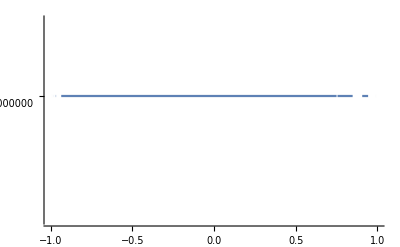

```mathematica
Plot[(0.03125 2.718281828459045^((0.-1.5707963267948966 ⅈ) (2.+2 ε)) (1.+2.718281828459045^((0.+3.141592653589793 ⅈ) ε))^2)/((0.125+0. ⅈ)+0.03125 2.718281828459045^((0.-3.141592653589793 ⅈ)-(0.+3.141592653589793 ⅈ) (1.+ε))+0.03125 2.718281828459045^((0.+3.141592653589793 ⅈ)-(0.+3.141592653589793 ⅈ) (1.+ε))+0.03125 2.718281828459045^((0.-3.141592653589793 ⅈ)+(0.+3.141592653589793 ⅈ) (1.+ε))+0.03125 2.718281828459045^((0.+3.141592653589793 ⅈ)+(0.+3.141592653589793 ⅈ) (1.+ε))),{ε,-1,1}]
```

### Identity gate using error-prone Ising interaction (Y input)

```mathematica
ε=.;

(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1, s2 *)
mout=RandomInteger[1,2];

(* Initialize the density matrix for 3 qubits *)
ρI=AF[ρ[KetY[0]]];
ρT=AF[ρI⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12=AF[ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]⊗𝕀];
ZZ23=AF[ⅇ^((ⅈ π)/4)𝕀⊗MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]];
UZZ=ZZ12.ZZ23;
ρZZ=Chop[UZZ.ρT.Adj[UZZ]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2},Proj.ρZZ.Proj]/Tr[Proj.ρZZ.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Input:",ρI//MatrixForm//N];
Print["Output:",ρOut//MatrixForm//N]
```

Measurement outcomes = {1,0}

Input:(0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)

Output:((0.03125 2.71828^((0.-3.14159 ⅈ) ε) (1.+2.71828^((0.+3.14159 ⅈ) ε))^2)/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))) | -((0.+0.03125 ⅈ) 2.71828^((0.-3.14159 ⅈ) ε) (1.+2.71828^((0.+3.14159 ⅈ) ε))^2)/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε])))
((0.+0.03125 ⅈ) 2.71828^((0.-3.14159 ⅈ) ε) (1.+2.71828^((0.+3.14159 ⅈ) ε))^2)/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))) | (0.03125 2.71828^((0.-3.14159 ⅈ) ε) (1.+2.71828^((0.+3.14159 ⅈ) ε))^2)/(0.03125 2.71828^((0.-3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)-(0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.+1.5708 ⅈ) (1.+ε)-(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.0625 2.71828^((0.-1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.-3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))+0.03125 2.71828^((0.+3.14159 ⅈ)+(0.+1.5708 ⅈ) (1.+ε)+(0.+1.5708 ⅈ) (1.+Conjugate[ε]))))

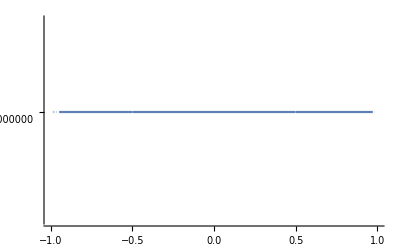

```mathematica
Plot[-(((0.25+3.061616997868383*^-17 ⅈ) (1.+ⅇ^((0.+3.141592653589793 ⅈ) ε))^2)/((0.5+6.123233995736766*^-17 ⅈ)+1. ⅇ^((0.+3.141592653589793 ⅈ) ε)+(0.5-6.123233995736765*^-17 ⅈ) ⅇ^((0.+6.283185307179586 ⅈ) ε))),{ε,-1,1}]
```

### Identity gate using error-prone Ising interaction (revisited)

```mathematica
ε=0.2;

(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1, s2 *)
mout=RandomInteger[1,2];

(* Initialize the density matrix for 3 qubits *)
(*ρI=AF[Chop[ρ[RandomKet1]]];*)
ρI=AF[ρ[KetY[0]]];
ρT=AF[ρI⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12ErrFree=AF[ⅇ^((ⅈ π)/4)MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]⊗𝕀];
ZZ12Err=-I Pi/4 AF[ⅇ^((ⅈ π)/4)AF[s[3]⊗s[3]].MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]⊗𝕀];
ZZ23ErrFree=AF[ⅇ^((ⅈ π)/4)𝕀⊗MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]];
ZZ23Err=-I Pi/4 AF[ⅇ^((ⅈ π)/4)𝕀⊗AF[s[3]⊗s[3]].MatrixExp[-I Pi/4 AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]]];
(*UZZ=ZZ12.ZZ23;*)
UZZErrFree=ZZ12ErrFree.ZZ23ErrFree;
UZZErr=ZZ12ErrFree.ZZ23Err+ZZ12Err.ZZ23ErrFree;
ρZZErrFree=Chop[UZZErrFree.ρT.Adj[UZZErrFree]];
ρZZErr=Chop[UZZErrFree.ρT.Adj[UZZErr]+UZZErr.ρT.Adj[UZZErrFree]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2},Proj.ρZZErr.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOutErr=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Input:",ρI//MatrixForm//N];
Print["Output:",ρOutErr//MatrixForm//N]
```

Measurement outcomes = {0,1}

Input:(0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)

Output:(-0.392699 | 0.+0.392699 ⅈ
0.-0.392699 ⅈ | -0.392699)

### Identity gate using error-prone Ising interaction (general input)

```mathematica
θ=.;
φ=.;
ε=.;

(* Initialize the input qubit *)
ρIn=FullSimplify[ComplexExpand[AF[ρ[Exp[I φ/2]Ket1[θ,φ]]]]];
Print["Input:",ρIn//MatrixForm];

(* Prepare cluster state *)
ρ0=AF[ρ[KetX[0]]];
ρT=AF[ρIn⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12=AF[ⅇ^((ⅈ π)/4)(MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]])⊗𝕀];
ZZ23=AF[ⅇ^((ⅈ π)/4)𝕀⊗(MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]])];
UZZ=ZZ12.ZZ23;
ρZZ=UZZ.ρT.Adj[UZZ];

Do[
(* Carry out the Pauli-X measurement on qubit 1, 2 *)
Proj=AF[PX[s1]⊗PX[s2]⊗𝕀] ;
ρM=PTr[{1,2},Proj.ρZZ.Proj]/Tr[Proj.ρZZ.Proj];

(* Drop the byproduct operator from the output *)
Byproduct=MatrixPower[s[1],s2].MatrixPower[s[3],s1];
ρOut=Byproduct.ρM.Adj[Byproduct];

Prob=FullSimplify[ComplexExpand[Chop[Tr[ρOut]]]];

(* Calculate the Fidelity *)
Fidelity=FullSimplify[ComplexExpand[Chop[Tr[ρIn.ρOut]]]];
Print["For (s_1,s_2)=(", s1,",",s2,"), Fidelity = ",Fidelity, ", Prob = ",Prob],
{s1,0,1},{s2,0,1}]
```

Input:(Cos[θ/2]^2 | 1/2 ⅇ^(-ⅈ φ) Sin[θ]
1/2 ⅇ^(ⅈ φ) Sin[θ] | Sin[θ/2]^2)

For (s_1,s_2)=(0,0), Fidelity = 1, Prob = 1

For (s_1,s_2)=(0,1), Fidelity = -(2 (-1+Sin[(π ε)/2] Sin[θ] Sin[φ])^2)/(-3+Cos[π ε]+4 Sin[(π ε)/2] Sin[θ] Sin[φ]), Prob = 1

For (s_1,s_2)=(1,0), Fidelity = 1, Prob = 1

For (s_1,s_2)=(1,1), Fidelity = (2 (1+Sin[(π ε)/2] Sin[θ] Sin[φ])^2)/(3-Cos[π ε]+4 Sin[(π ε)/2] Sin[θ] Sin[φ]), Prob = 1

### Identity gate using error-prone Ising interaction (general input; average over measurement outcomes)

```mathematica
θ=.;
φ=.;
ε=.;

(* Initialize the input qubit *)
ρIn=FullSimplify[ComplexExpand[AF[ρ[Exp[I φ/2]Ket1[θ,φ]]]]];
Print["Input:",ρIn//MatrixForm];

(* Prepare cluster state *)
ρ0=AF[ρ[KetX[0]]];
ρT=AF[ρIn⊗ρ0⊗ρ0];

(* Entangle qubits via ZZ gate *)
ZZ12=AF[ⅇ^((ⅈ π)/4)(MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]])⊗𝕀];
ZZ23=AF[ⅇ^((ⅈ π)/4)𝕀⊗(MatrixExp[-I Pi/4(1+ε)AF[s[3]⊗s[3]]].MatrixExp[I Pi/4 AF[s[3]⊗𝕀]].MatrixExp[I Pi/4 AF[𝕀⊗s[3]]])];
UZZ=ZZ12.ZZ23;
ρZZ=UZZ.ρT.Adj[UZZ];

(* Average the output over measurement outcomes*)
ρOut=ZeroMatrix[2];
Do[
(* Carry out the Pauli-X measurement on qubit 1, 2 *)
Proj=AF[PX[s1]⊗PX[s2]⊗𝕀] ;
ρM=PTr[{1,2},Proj.ρZZ.Proj]/Tr[Proj.ρZZ.Proj];

(* Remove the byproduct operator from the output *)
Byproduct=MatrixPower[s[1],s2].MatrixPower[s[3],s1];
ρO=FullSimplify[ComplexExpand[Chop[Byproduct.ρM.Adj[Byproduct]]]];
Prob=FullSimplify[ComplexExpand[Chop[Tr[ρO]]]];
ρOut+=Prob*ρO,
{s1,0,1},{s2,0,1}];
ρOut=ρOut/4;

(* Calculate the Fidelity *)
Fidelity=FullSimplify[ComplexExpand[Chop[Tr[ρIn.ρOut]]]];
Print["Fidelity = ",Fidelity]
```

Input:(Cos[θ/2]^2 | 1/2 ⅇ^(-ⅈ φ) Sin[θ]
1/2 ⅇ^(ⅈ φ) Sin[θ] | Sin[θ/2]^2)

Fidelity = (99-40 Cos[π ε]+5 Cos[2 π ε]+4 (13+Cos[π ε]) Cos[2 θ] Sin[(π ε)/2]^2+8 (13+Cos[π ε]) Cos[2 φ] Sin[(π ε)/2]^2 Sin[θ]^2)/(16 ((-3+Cos[π ε])^2-16 Sin[(π ε)/2]^2 Sin[θ]^2 Sin[φ]^2))

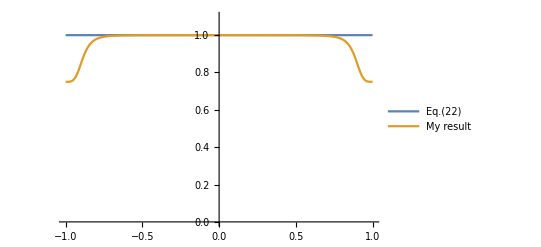

```mathematica
θ=Pi/2;
φ=Pi/2*0.99;
FormulaA=((1-Cos[2φ])(1-Cos[2θ])(1-Cos[π ε])+4Cos[π ε]+12)/16;
FormulaB=-(Sec[(π ε)/2]^2 (-32 Cos[(π ε)/2]^2 (99-40 Cos[π ε]+5 Cos[2 π ε])-32 (13+Cos[π ε]) Sin[π ε]^2 (Cos[2 θ]+2 Cos[2 φ] Sin[θ]^2)))/(256 (15-8 Cos[π ε]+Cos[2 π ε]-2 Cos[π ε-2 θ]+4 Cos[2 θ]-2 Cos[π ε+2 θ]+16 Cos[2 φ] Sin[(π ε)/2]^2 Sin[θ]^2));
Plot[{FormulaA,FormulaB},{ε,-1,1},PlotRange->{0,1.1},PlotLegends->{"Eq.(22)","My result"}]
```

Can we come up with a clear explanation for why the fidelity is 1 for the case of error prone Ising with initial states along + /-y?
One way to explain this is that for Ising there is a symmetry in the circuit diagram which somehow leaves the fidelity = 1.